```mathematica
Import["/home/syang/Downloads/MG5_aMC_v2_6_5/EventTools.m"]
```

```mathematica
data=Get["/home/syang/Downloads/MG5_aMC_v2_6_5/ppdecay/Events/run_01/output"]
```

{{{-11,-49.5692,0.0695196,89.4034,102.226},{12,-104.867,-17.0319,581.784,591.405},{5,21.3498,-10.0506,19.0067,30.6622},{1,21.3362,45.229,42.7922,65.8184},{-2,-2.97826,-27.061,69.0358,74.2099},{-5,114.728,8.84495,22.5084,117.344}},9998,{{-13,-39.3724,-33.1598,-29.0278,59.0963},4,{-5,9.32733,-46.8975,7.0367,48.5591}}}
 |  |  |  |

```mathematica
datal={};
Table[If[Abs[data[[i,j,1]]]==11||Abs[data[[i,j,1]]]==13,AppendTo[datal,data[[i,j]]]],{j,6},{i,data//Length}];
```

```mathematica
datal
```

{{-11,-49.5692,0.0695196,89.4034,102.226},{-13,-79.0673,-3.66694,-123.937,147.056},9996,{13,17.8593,26.0267,18.9909,36.8374},{11,54.6187,75.7274,29.1086,97.8016}}
 |  |  |  |

datal

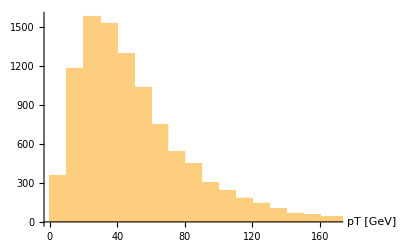

```mathematica
hisData1=pT/@datal[[All,2;;5]];
Histogram[hisData1,50,AxesLabel->{"pT [GeV]"}]
```

```mathematica
datanu={};
Table[If[Abs[data[[i,j,1]]]==12||Abs[data[[i,j,1]]]==14,AppendTo[datanu,-Total[Drop[data[[i]],{j}]]]],{j,1,6},{i,1,data//Length}];
```

```mathematica
datanu
```

$RecursionLimit::reclim2: Recursion depth of 4096 exceeded during evaluation of MakeBoxes[Insert,StandardForm].

$RecursionLimit::reclim2: Recursion depth of 4096 exceeded during evaluation of MakeBoxes[Insert[Insert[Insert[Insert[Insert[Insert[Insert[«2»],{«5»}],{0,3.60004×10^-10,4.99995×10^-10,-802.602,-888.229}],{0,-1.×10^-9,-2.00003×10^-9,266.277,-698.055}],{0,«3»,-1102.24}],{«1»}],{«1»}],«12»].

$RecursionLimit::reclim2: Recursion depth of 4096 exceeded during evaluation of MakeBoxes[{0,-1.00002×10^-10,-4.00013×10^-10,180.37,-397.619},StandardForm].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

```mathematica
hisData2=ET/@datanu[[All,2;;5]];
```

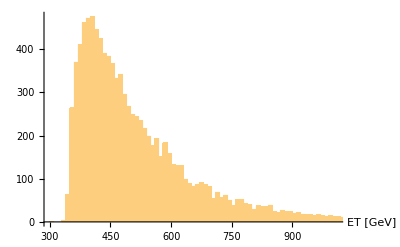

```mathematica
Histogram[hisData2,150,AxesLabel->{"ET [GeV]"}]
```

```mathematica
ETLepton=ET/@datal[[All,2;;5]];
ETnu=hisData2;
angle=Table[Δϕ[{datal[[i]],datanu[[i]]}],{i,1,datal//Length}];
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

```mathematica
mt=Sqrt[2*ETLepton*ETnu*(1-Cos[angle])];
```

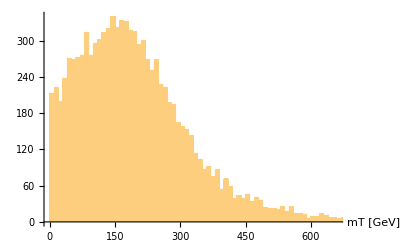

For::argt: For called with 2 arguments; 3 or 4 arguments are expected.

{}

{}

{11,-39.8726,-26.8409,-0.619955,48.0692}

{}

```mathematica
Histogram[mt,150,AxesLabel->{"mT [GeV]"}]
```